### A description of ScanMaster's data structure

#### Basic structure

The data recorded with ScanMaster is written as zipped xml. The classes that ScanMaster uses to represent and manipulate the data are available to Mathematica via the .NET/Link. The code is on the .NET side, but you can use it directly from within Mathematica. You first need to load the SEDM`SharedCode` package, and call initalizeSharedCode[]...

```mathematica
AppendTo[$Path,"C:\Program Files\ScanMaster\MathematicaFiles\SEDM3\SEDM3"];
AppendTo[$Path,"C:\Program Files\ScanMaster\bin\Microcavity"];
```

```mathematica
<<SEDM3`EDMSuite`
initialiseSharedCode[]
```

Here is a brief description of the objects that make up the data structure.
 
Data.Scans.TOF: The basic object in the data structure is a TOF (a time of flight profile). It is the result of a single detector looking at a single pulse from the source.
Data.Scans.Shot: A Shot is the set of measurements associated with a single pulse from the source. It contains a list of TOF's. This becomes useful if (for example) there is more than one detector measuring time-of-flight profiles.
Data.Scans.ScanPoint: A ScanPoint represents a single point in a scan. It holds a list of all the shots obtained at that point (maybe we took a number of shots at each point in the scan in order to improve the signal-to-noise). The shots are stored in two sets, one called the OnShots and the other the OffShots. This becomes useful when, at each point in the scan, shots are taken with some parameter switching on and off. When using a profile that doesn't involve such a switch, the OffShots will be empty. As well as the Shots, a ScanPoint also holds the values of any analog channels that were measured (e.g. reference cavity), and it holds the value of the scan parameter for this point in the scan.
Data.Scans.Scan: This is the set of all the ScanPoints.

One other object we need is a ScanSerializer. The ScanSerializer class contains the methods that allows for writing and reading the data. You have to begin by making a ScanSerializer using Mathematica's NETNew, like this...

```mathematica
serializer = NETNew["Data.Scans.ScanSerializer"];
```

You now have a ScanSerializer and can use it to read in data that has been stored as zipped xml, by calling the ScanSerializer method 'public Scan DeserializeScanFromZippedXML(String zipFilePath, String scanFileName)'. Use the "@" notation to access the public methods and fields of a class. The file that holds the scan-averaged data within the .zip is always called average.xml. So, to retrieve a scan...

```mathematica
scan1=serializer@DeserializeScanFromZippedXML["z:\\data\\16-11-15\\Microcavity\\15Nov1600.zip","scan_3.xml"]
```

«NETObject[Data.Scans.Scan]»

You get back an object whose type is Data.Scans.Scan (we'll often just call this a Scan, leaving out the Data.Scans namespace). To get used to the data structure, we can think about how to extract a single time-of-flight profile. Let's suppose we want the time-of-flight profile recorded at the first detector at point 188 in the scan. 

The Scan contains an array of ScanPoints, which you can get using the Points property of the Scan class. To get an individual point, like point 188 use

```mathematica
scan1@Points[188]
```

«NETObject[Data.Scans.ScanPoint]»

This returns a ScanPoint. We can get the list of all the OnShots recorded at this ScanPoint. There was only one, and we get it by setting the index to zero...

```mathematica
scan1@Points[188]@OnShots[0]
```

«NETObject[Data.Shot]»

Now we have a Shot. A Shot contains a list of TOF's, and we want the Shot recorded at the first (and only) detector. You can get the list of TOF's using the TOFs property, and set the index to zero to get the first (and only in this case) element.

```mathematica
scan1@Points[188]@OnShots[0]@TOFs[0]
```

«NETObject[Data.TOF]»

Now we have a TOF. To get the y-data, use the Data property, and to get the time-data use the Times property. Both return lists of numbers. So, here's the time-of-flight profile we were looking for.

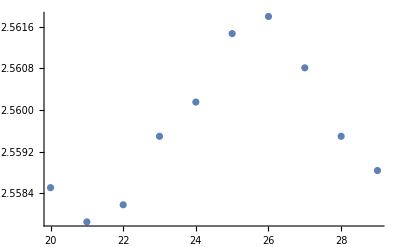

```mathematica
ListPlot[{scan1@Points[188]@OnShots[0]@TOFs[0]@Times,scan1@Points[188]@OnShots[0]@TOFs[0]@Data}//Transpose]
```

#### Things you can do with a TOF

Let's make a named reference to the TOF we looked at already.

```mathematica
tof188 = scan1@Points[188]@OnShots[0]@TOFs[0]
```

«NETObject[Data.TOF]»

A TOF has the following properties: Length, GateStartTime & ClockPeriod (all in μs).

```mathematica
tof188@Length
tof188@GateStartTime
tof188@ClockPeriod
```

10

20

1

There are methods for integrating the counts in the TOF, either over its entire range, Integrate[] , or over a range, Integrate[double startTime, double endTime] :-

```mathematica
tof188@Integrate[]
tof188@Integrate[20,30]
```

25.5966

23.0379

#### Things you can do with a Shot

Here's a reference to a Shot.

```mathematica
shot188=scan1@Points[188]@OnShots[0]
```

«NETObject[Data.Shot]»

You can integrate a Shot. This is just a convenience method which gets handed down to the Integrate method of the TOF. Since a Shot holds a list of TOFs you need to give the index of the TOF to be integrated as an argument - Integrate[int index, double startTime, double endTime]:-

```mathematica
shot188@Integrate[0,1400,1600]
```

0.

#### Things you can do with a ScanPoint

Here's a reference to a ScanPoint.

```mathematica
point188 = scan1@Points[188]
```

«NETObject[Data.Scans.ScanPoint]»

A ScanPoint has three lists, a list of OnShots, a list of OffShots and a list of Analogs. It also keeps a record of the ScanParameter (e.g. the value of the voltage being sent to the laser). The present ScanPoint has no OffShot so the list is empty and we get an error when we ask for the first element. The ScanPoint has two analog readings associated with it (in this case from our two cavities).

```mathematica
point188@OnShots[0]
point188@OffShots[0]
{point188@Analogs[0],point188@Analogs[1]}
point188@ScanParameter
```

«NETObject[Data.Shot]»

NET::netexcptn: A .NET exception occurred: System.ArgumentOutOfRangeException: Index was out of range. Must be non-negative and less than the size of the collection.
Parameter name: index
   at System.Collections.ArrayList.get_Item(Int32 index).

$Failed

{0.223434,0.159229}

-3.115

If the list of OnShots or OffShots contains more than one element, it is probably because we took a bunch of Shots at each ScanPoint in order to improve the signal-to-noise. In that case, we most likely want to form the average over all the Shots at this ScanPoint. Use the AverageOnShot and AverageOffShot properties.

```mathematica
point188@AverageOnShot
point188@AverageOffShot
```

«NETObject[Data.Shot]»

«NETObject[Data.Shot]»

A ScanPoint contains methods IntegrateOn[int index, double startTime, double endTime] and IntegrateOff[int index, double startTime, double endTime]. For example, the IntegrateOn method integrates under all the OnShots at this ScanPoint for the detector specified by the index, between the startTime and endTime:-

```mathematica
point188@IntegrateOn[0,20,30]
```

23.0379

#### Things you can do with a Scan

Two very useful methods are
public double[] GetTOFOnIntegralArray(int index, double startTime, double endTime)  and 
public double[] GetTOFOffIntegralArray(int index, double startTime, double endTime)

They iterate over the list of ScanPoints, doing the integral of the Shot for the detector specified by index, between startTime and endTime, at every ScanPoint. This provides what we often call the 'gated spectrum'. If we set the gates appropriately we get a nice spectrum; if we set them outside the time-region where there is any signal, we just get noise.

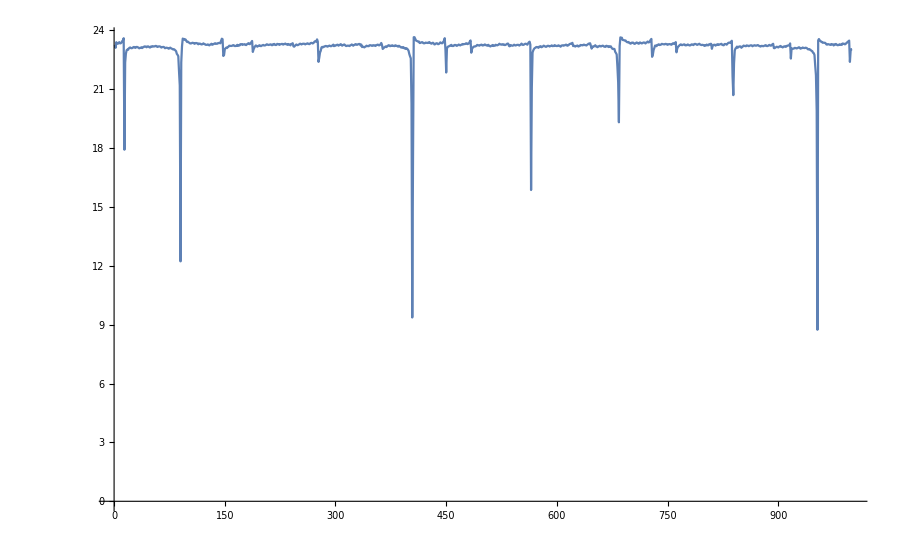

```mathematica
ListPlot[scan1@GetTOFOnIntegralArray[0,20,30],PlotRange->All,PlotJoined->True]
```

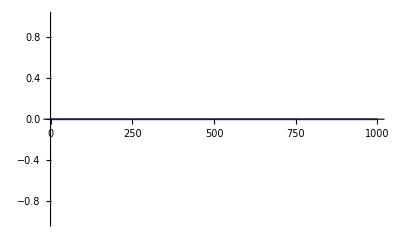

```mathematica
ListPlot[scan1@GetTOFOnIntegralArray[0,1700,1900],PlotRange->All,PlotJoined->True]
```

Here's a zoom into an interesting part of the spectrum

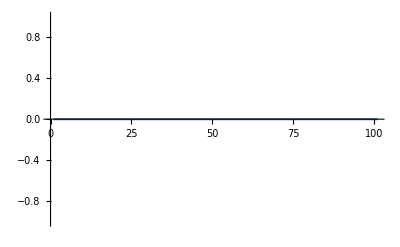

```mathematica
ListPlot[(scan1@GetTOFOnIntegralArray[0,1300,1700])⟦Range[150,250]⟧,PlotRange->All,PlotJoined->True]
```

There is a ScanParameterArray property, which returns the list of the ScanParameter values at each ScanPoint. Useful if you want to make a plot versus the ScanParameter value:

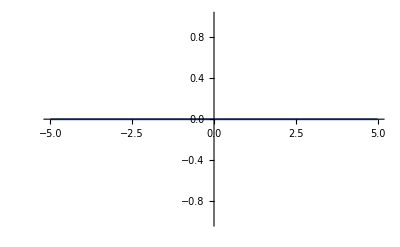

```mathematica
ListPlot[{scan1@ScanParameterArray,scan1@GetTOFOnIntegralArray[0,1300,1700]}//Transpose,PlotRange->All,PlotJoined->True]
```

There is a method public double[] GetDifferenceIntegralArray(int index, double startTime, double endTime) that can be used to take the difference between the 'on spectrum' and the 'off spectrum', appropriately gated.

To obtain the average of the shots between some particular values of the ScanParameter, use public Shot GetGatedAverageOnShot(double lowGate, double highGate) and public Shot GetGatedAverageOffShot(double lowGate, double highGate).

```mathematica
avShot=scan1@GetGatedAverageOnShot[-3.5,-3]
```

«NETObject[Data.Shot]»

This gives you a Shot, which is the average of all the Shots within the specified gates. You can then obtain the corresponding TOF for the first detector in the usual way.

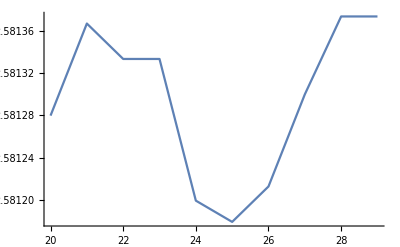

```mathematica
ListPlot[{avShot@TOFs[0]@Times,avShot@TOFs[0]@Data}//Transpose,PlotJoined->True]
```

If you gate out a region of the spectrum where there is no signal, you get noise!

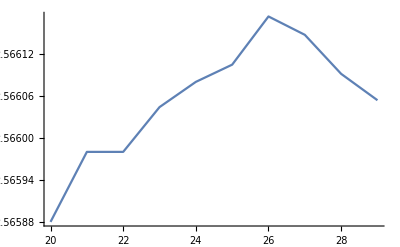

```mathematica
avShot=scan1@GetGatedAverageOnShot[-1,1];
ListPlot[{avShot@TOFs[0]@Times,avShot@TOFs[0]@Data}//Transpose,PlotJoined->True]
```

We also want to get to the analog signals as a function of ScanParameter. Use public double[] GetAnalogArray(int index). The index specifies which analog channel to get.

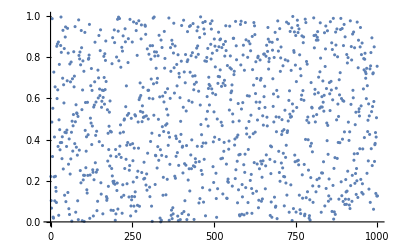

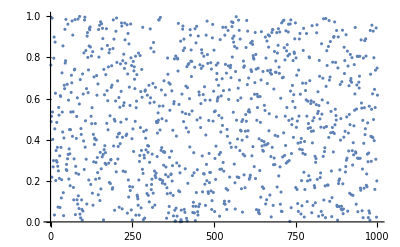

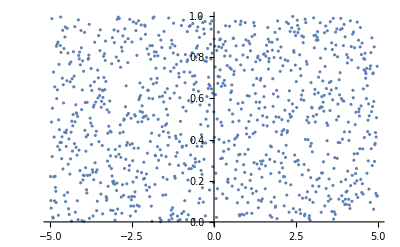

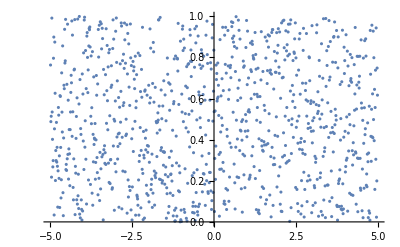

```mathematica
ListPlot[scan1@GetAnalogArray[0]]
ListPlot[scan1@GetAnalogArray[1]]
ListPlot[{scan1@ScanParameterArray,scan1@GetAnalogArray[0]}//Transpose]
ListPlot[{scan1@ScanParameterArray,scan1@GetAnalogArray[1]}//Transpose]
```